# Lindblad master equation

Solving  quantum Liouvillian master equation

## Example Content

We solve the Lindblad master equation: ∂_t ρ=-i[H,ρ]+∑_i γ_i(L_i ρ L_i^†-1/2{L_i^†L_i,ρ}) with ρ the density matrix, L_i th jump operator and γ_i its corresponding damping rate.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

PacletObject[…]

Initial state:

```mathematica
ρ0=QuantumState[{Cos[π/8],Exp[ⅈ π/4]Sin[π/8]}]
```

QuantumState[…]

Set Ω, γ and N parameters in finite temperature amplitude damping mechanism:

```mathematica
Ω=50;γ=1;n=3;
```

Setting up Hamiltonian, list of jump operator and their corresponding rates

```mathematica
H=Ω/2 QuantumOperator["Z"];
Ls=QuantumOperator/@{"J-","J+"};
γs=γ{n+1,n};
```

With H a quantum operator as Hamiltonian, L_i the jump operators, and γ_i the corresponding rates, determine the state:

```mathematica
ρt=QuantumEvolve[H,Ls,γs,ρ0,{t,0,1}]
```

QuantumState[…]

Plot the evolution:

```mathematica
Show[QuantumState["UniformMixture"]["BlochPlot"],ParametricPlot3D[Evaluate@Re@ρt[t]["BlochVector"],{t,0,1}]]
```

-Graphics3D-

One can also incorporate the rates into the definition of operators as √γ_i L_iand have only  QuantumEvolve[H,{L1,L2,...},QuantumState[...],{t,t_i,t_f}]

```mathematica
ρt2=QuantumEvolve[H,√γs Ls,ρ0,{t,0,1}]
```

QuantumState[…]

Plot the evolution:

```mathematica
Show[QuantumState["UniformMixture"]["BlochPlot"],ParametricPlot3D[Evaluate@Re@ρt2[t]["BlochVector"],{t,0,1}]]
```

-Graphics3D-

One can also create Liouvillian (dρ/dt=ℒρ)

```mathematica
ℒ= QuantumOperator["Liouvillian"[H,Ls,γs]]
```

QuantumOperator[…]

Evolution super-operator: ρ_t = Exp[ℒt]ρ_0

```mathematica
expℒ=QuantumEvolve[I ℒ,None,{t,0,1}];
ρt3[t_]=expℒ[t][ρ0]
```

QuantumState[…]

Plot the evolution:

```mathematica
Show[QuantumState["UniformMixture"]["BlochPlot"],ParametricPlot3D[Evaluate@Re@expℒ[ρ0]["BlochVector"],{t,0,1}]]
```

-Graphics3D-

Since the Liouvillian is time-independent, one can also do this:

```mathematica
ρt4[t_]=Exp[ ℒ t][ρ0]
```

QuantumState[…]

Plot the evolution:

```mathematica
Show[QuantumState["UniformMixture"]["BlochPlot"],ParametricPlot3D[Evaluate@Re@ρt4[t]["BlochVector"],{t,0,1}]]
```

-Graphics3D-

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

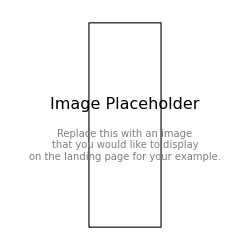

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

Dissipation

Quantum master equation

Lindblad master equation

Quantum Liouvillian master equation

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.